## Growth Function Normalization

```mathematica
(*********************************************)
Print[Style["Parameters",Orange]]
(*********************************************)
 w1 =-1;
 w2 =-0.1;
 w3 =-0.5;
 w4 =-4/5;
 ΩDE0 =0.73;
Ωk0=0;
 Ωm0 =0.27;
 Ωr0 =8.09*10^-5;
h=0.71;
 (*H0 =(100 h)/300000;*)H0=100 h;
Ωm0s =1; 
Ωr0s =8.09*10^-5*(1/1.2)^2;
(*Ωr0s=0;*)
```

Parameters

```mathematica
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at equality",Orange]]
(*********************************************)
HL0=H20=H30=H40=H0;
Hs0=H0*1.2;
(*
Hs0=(HL0 √(Ωm0  aeq^-3+ Ωr0  aeq^-4+ ΩDE0  aeq^(-3(1+ w1 ))))/(√(Ωm0s  aes^-3+ Ωr0s  aes^-4))
H20=(HL0 √(Ωm0  aeq^-3+ Ωr0  aeq^-4+ ΩDE0  aeq^(-3(1+ w1 ))))/(√(Ωm0 aeq^-3+ Ωr0 aeq^-4+ ΩDE0 aeq^(-3(1+ w2 ))))
H30=(HL0 √(Ωm0  aeq^-3+ Ωr0  aeq^-4+ ΩDE0  aeq^(-3(1+ w1 ))))/(√(Ωm0 aeq^-3+ Ωr0 aeq^-4+ ΩDE0 aeq^(-3(1+ w3 ))))
H40=(HL0 √(Ωm0  aeq^-3+ Ωr0  aeq^-4+ ΩDE0  aeq^(-3(1+ w1 ))))/(√(Ωm0 aeq^-3+ Ωr0 aeq^-4+ ΩDE0 aeq^(-3(1+ w4 ))))
*)
```

Intial conditions for Hubble constant, normalized at equality

```mathematica
(*********************************************)
Print[Style["Define Hubble functions",Orange]]
(*********************************************)
 Hs[a_]:=Hs0  √(Ωm0s a^-3+ Ωr0s a^-4);
 HL[a_]:=HL0  √(Ωm0 a^-3+ Ωr0 a^-4+ ΩDE0 a^(-3(1+w1)))
 H2[a_]:=H20 √(Ωm0 a^-3+ Ωr0 a^-4+ ΩDE0 a^(-3(1+w2)))
 H3[a_]:=H30 √(Ωm0 a^-3+ Ωr0 a^-4+ ΩDE0 a^(-3(1+w3)))
 H4[a_]:=H40 √(Ωm0 a^-3+ Ωr0 a^-4+ ΩDE0 a^(-3(1+w4)))
```

Define Hubble functions

```mathematica
(*********************************************)
Print[Style["Hubble distances",Orange]]
(*********************************************)
dHL[a]=1/HL[a];dH2[a]=1/H2[a];dH3[a]=1/H3[a];dH4[a]=1/H4[a];
```

Hubble distances

```mathematica
(*********************************************)
Print[Style["Define k of a",Orange]]
(*********************************************)
kL[a_]= HL[a];ks[a_]= Hs[a];kDE2[a_]= H2[a];kDE3[a_]= H3[a];kDE4[a_]= H4[a];
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k== H2[a2],a2];*)
```

Define k of a

```mathematica
(*********************************************)
Print[Style["Define growth factors",Orange]]
(*********************************************)
Growths[a_]:= 5/2 Ωm0s  Hs[a]/H0  NIntegrate[1/(x^3(Hs[x]/H0)^3),{x,0,a}];
GrowthL[a_]:= 5/2 Ωm0  HL[a]/H0  NIntegrate[1/(x^3(HL[x]/H0)^3),{x,0,a}];
GrowthDE2[a_]:=5/2 Ωm0  H2[a]/H0  NIntegrate[1/(x^3(H2[x]/H0)^3),{x,0,a}];
GrowthDE3[a_]:=5/2 Ωm0  H3[a]/H0  NIntegrate[1/(x^3(H3[x]/H0)^3),{x,0,a}];
GrowthDE4[a_]:=5/2 Ωm0  H4[a]/H0  NIntegrate[1/(x^3(H4[x]/H0)^3),{x,0,a}];
```

Define growth factors

Plot k of a

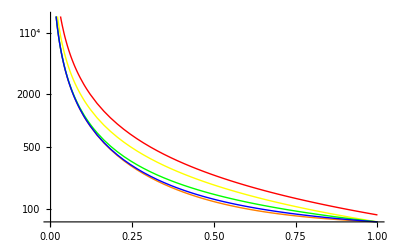

```mathematica
(*********************************************)
Print[Style["Plot k of a",Orange]]
(*********************************************)
LogPlot[{ks[a],kL[a],kDE2[a],kDE3[a],kDE4[a]},{a,10^-3,1},PlotStyle->{Red,Orange,Yellow,Green,Blue}]
```

Plot growth factors of a for LCDM

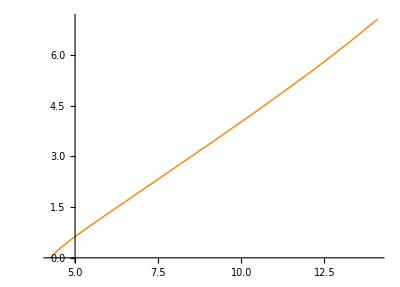

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for LCDM",Orange]]
(*********************************************)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {5,0},PlotStyle->{Orange}]
```

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",Orange]]
(*********************************************)
Plot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a]},{a,0,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}];
LogLogPlot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", ""}]
```

Plot growth factors of a for all models

LogLogPlot::optx: Unknown option PlotLegend → {"sCDM", ""} in {Growths[a], GrowthL[a], GrowthDE2[a], GrowthDE3[a], GrowthDE4[a]}, {a, 1/10^4, 1}, PlotStyle → {Red, Orange, Yellow, Green, Blue}, AxesLabel → {a, .

LogLogPlot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a]},{a,1/10^4,1},PlotStyle→{Red,Orange,Yellow,Green,Blue},AxesLabel→{a,D_+(a)},PlotLegend→{sCDM,}]

```mathematica
(*********************************************)
Print[Style["Tranform growth factors / Hubble distances of a to those of 1+z",Orange]]
(*********************************************)
GS[mn_]:=Growths[1/mn];GL[mn_]:=GrowthL[1/mn];GDE2[mn_]:=GrowthDE2[1/mn];GDE3[mn_]:=GrowthDE3[1/mn];GDE4[mn_]:=GrowthDE4[1/mn];
Lambdas[mn_]=1/Hs[1/mn];LambdaL[mn_]=1/HL[1/mn];Lambda2[mn_]=1/H2[1/mn];Lambda3[mn_]=1/H3[1/mn];Lambda4[mn_]=1/H4[1/mn];
```

Tranform growth factors / Hubble distances of a to those of 1+z

Plot Hubble distances

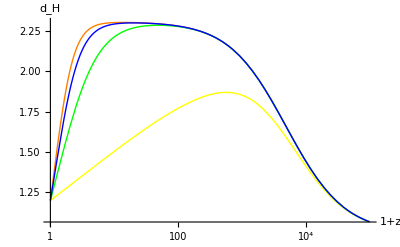

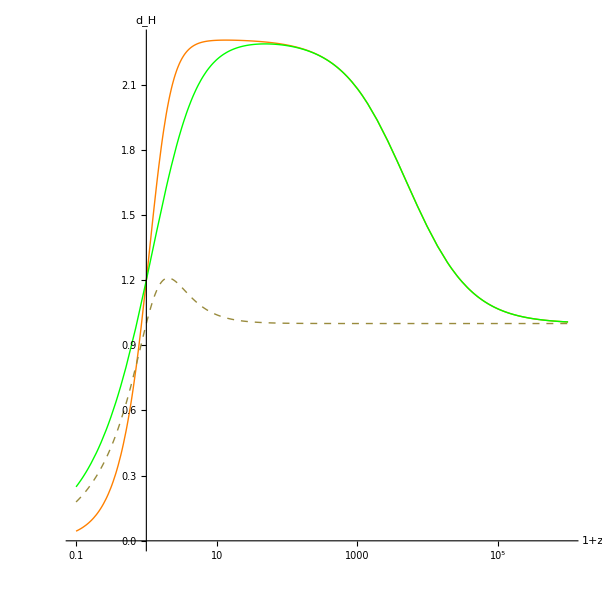

```mathematica
(*********************************************)
Print[Style["Plot Hubble distances",Orange]]
(*********************************************)
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda2[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],Lambda4[mn]/Lambdas[mn]},{mn,1,10^5},PlotStyle->{Orange,Yellow,Green,Blue},AxesLabel->{"1+z","d_H"}]
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],LambdaL[mn]/Lambda3[mn]},{mn,0.1,10^6},PlotStyle->{Orange,Green,Dashed},AxesLabel->{"1+z","d_H"},AxesOrigin-> {1,0},AspectRatio->1]
```

Plot growth factors in terms of 1+z

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

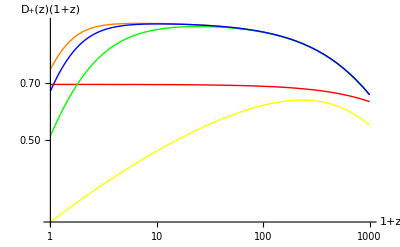

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

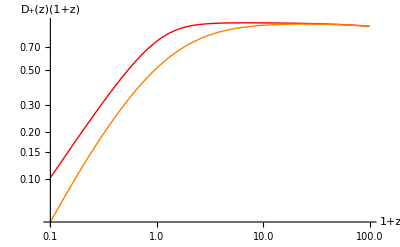

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

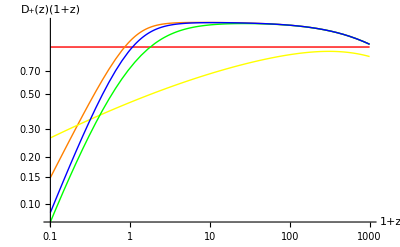

```mathematica
(*********************************************)
Print[Style["Plot growth factors in terms of 1+z",Orange]]
(*********************************************)
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn)GDE2[mn],(mn)GDE3[mn],(mn)GDE4[mn]},{mn,1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
LogLogPlot[{(mn)GL[mn],(mn)GDE3[mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Green},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
(*Another normalization*)
LogLogPlot[{GS[mn]/GS[mn],GL[mn]/GS[mn],GDE2[mn]/GS[mn],GDE3[mn]/GS[mn],GDE4[mn]/GS[mn]},{mn,0.1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
(*LogLogPlot[{1,GL[mn]/GS[mn],GDE2[mn]/GS[mn],GDE3[mn]/GS[mn],GDE4[mn]/GS[mn]},{mn,0.1,100},AxesLabel-> {"1+z","D_+(z)(1+z)"}]*)
```